# Noisy GHZ state distillation via alternating schemes

## Description

Author: Aron Rozgonyi; email: rozgonyi.aron@wigner.hu
Corresponding article:

In this notebook, we perform the following tasks:
* Simulate a 3-qubit entangled state distillation protocol
* Formulate analytical unitary matrices for aforementioned protocol   
* The goal is to transform a noisy entangled state into the Greenberger-Horne-Zeilinger (GHZ) state within a reasonable number of iteration of the protocol

protocol steps: 
(0) three parties are interconnected with a shared noisy entangled 3-qubit GHZ state
(1) The parties begin by sharing the noisy entangled state and its identical replica, referred to as the “flag.”
(2) Each party applies uniform unitary operations on their respective qubits.
(3) Projective measurements are performed on the flag qubits.
(4) Using a classical channel, the parties communicate and agree that only scenarios resulting in a measurement outcome of zero are acceptable. 
They discuss their individual measurement results, and if any other outcome is obtained, the protocol is cancelled.
(5) If necessary, the protocol proceeds to the next iteration to further enhance the entanglement.

-Graphics-

## Definitions

```mathematica
(********************************************************)
(***** DEFINITION OF FUNCTIONS USED IN THE NOTEBOOK ******)
(********************************************************)

(* Pauli operators *)
Ι=PauliMatrix[0];
X=PauliMatrix[1];
Y=PauliMatrix[2];
Z=PauliMatrix[3];

(* Measurement projectors *)
M0=Outer[Times, {1,0},Conjugate[{1,0}]];
M=KroneckerProduct@@{Ι,M0,Ι,M0,Ι,M0};
M′=KroneckerProduct@@{Ι,Ι,Ι,M0,M0,M0};
M1=Outer[Times, {0,1},Conjugate[{0,1}]];
M′1=KroneckerProduct@@{Ι,Ι,Ι,M1,M1,M1};

(* Entangled States *)
S0={1,0};
S1={0,1};
GHZ=(Flatten@KroneckerProduct[S0,S0,S0]+Flatten@KroneckerProduct[S1,S1,S1])/Sqrt[2];
cGHZ=Conjugate[GHZ]; 
GHZL=N@(Flatten@KroneckerProduct[S0,S0,S0]+0.3*Flatten@KroneckerProduct[S1,S1,S1])/Sqrt[2];
W=N@(Flatten@KroneckerProduct[S0,S0,S1]+Flatten@KroneckerProduct[S0,S1,S0]+Flatten@KroneckerProduct[S1,S0,S0])/Sqrt[3];
ρGHZ=SparseArray@Outer[Times, GHZ,Conjugate[GHZ]];
ρGHZL=SparseArray@Outer[Times, GHZL,Conjugate[GHZL]];
ρW=SparseArray@Outer[Times, W,Conjugate[W]];

(* I_2 noise *)
NoiseMatrix[Ν′_]:=ReplacePart[Table[0,{i,Ν′},{j,Ν′}],{{1,1}->1,{Ν′,Ν′}->1}]

(* CNOT gate *)
Ν=6;
basis=Tuples[{0,1},Ν];
basisS=Map["|"<>StringJoin[Map[ToString[#]&,#]]<>"⟩"&,Tuples[{0,1},Ν]];
CNOTket[i_,j_,list_]:=Block[{output=list},If[list⟦i⟧==0,output,output⟦j⟧=-output⟦j⟧+1;output]]
CNOTmatrix[i_,j_]:=Normal[SparseArray[Table[{n,Position[basis,CNOTket[i,j,basis⟦n⟧]]⟦1,1⟧}->1,{n,Length[basis]}],{Length[basis],Length[basis]}]]
Do[CNOT[i->j]=CNOTmatrix[i,j],{i,Ν},{j,Ν}]

(* SWAP GATE *)
Ν=6;
basis=Tuples[{0,1},Ν];
basisS=Map["|"<>StringJoin[Map[ToString[#]&,#]]<>"⟩"&,Tuples[{0,1},Ν]];
SWAP[i_,j_]:=Normal[SparseArray[Table[1+{k,
If[
Mod[Quotient[k,2^(Ν-i)],2]==Mod[Quotient[k,2^(Ν-j)],2],
k,
BitXor[BitXor[k,2^(Ν-i)],2^(Ν-j)]
]}->1,{k,0,2^Ν-1}],{2^Ν,2^Ν}]]

(* BASIS TRANSFORMATION *)
TRF= SWAP[3,4].SWAP[3,5].SWAP[2,4];

(* Partial Trace *)
PartialTrace[ρ_,dim_]:=Block[{Ν,ρs},
Ν=Log[2,Length[ρ]];
ρs=ArrayReshape[ρ,ConstantArray[2,2Ν]];
ArrayReshape[TensorContract[ρs,Map[{#,#+Ν}&,dim]],{2^(Ν-Length[dim]),2^(Ν-Length[dim])}]]
```

## Transforming GHZ-like pure state to GHZ state in 1 iteration

Constraints:
The amplitudes of the states |001⟩, |010⟩, |011⟩, |100⟩, |101⟩ and |110⟩ are all required to be zero.
The amplitudes of the states |000⟩ and |111⟩ are required to be equal.

### protocol with arbitrary unitary (step by step)

```mathematica
(* initial GHZ-like state *)
ψ0=Table[z[i],{i,1,8}]*{1,0,0,0,0,0,0,1}
```

{z[1],0,0,0,0,0,0,z[8]}

```mathematica
(* 2-qubit general unitary *)
U=Table[u[i,j],{i,1,4},{j,1,4}];
%//MatrixForm
```

(u[1,1] | u[1,2] | u[1,3] | u[1,4]
u[2,1] | u[2,2] | u[2,3] | u[2,4]
u[3,1] | u[3,2] | u[3,3] | u[3,4]
u[4,1] | u[4,2] | u[4,3] | u[4,4])

```mathematica
(* state prior to act with U unitary (Ket[1]) *)
ϕ1=Flatten[KroneckerProduct[ψ0,ψ0]] (* ordering 123456 *)
```

{z[1]^2,0,0,0,0,0,0,z[1] z[8],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,z[1] z[8],0,0,0,0,0,0,z[8]^2}

```mathematica
(* basis transformation *)
ϕ1SW=TRF.Flatten[KroneckerProduct[ψ0,ψ0]] (* ordering 142536 *)
```

{z[1]^2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,z[1] z[8],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,z[1] z[8],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,z[8]^2}

```mathematica
(* state subsequent to the unitary operation U (Ket[2]) *)
ϕ2SW=KroneckerProduct[U,U,U].ϕ1SW ;(* ordering 142536 *)
```

```mathematica
(* The indices of the basis states that yields a measurement outcome of '0' on qubits 456 *)
basisϕ=Tuples[{0,1},6];
Select[ basisϕ,#⟦2⟧+#⟦4⟧+#⟦6⟧==0&];
Select[Transpose[{Range[64],basisϕ}],#⟦2,2⟧+#⟦2,4⟧+#⟦2,6⟧==0&];
index000=Select[Transpose[{Range[64],basisϕ}],#⟦2,2⟧+#⟦2,4⟧+#⟦2,6⟧==0&]⟦All,1⟧
```

{1,3,9,11,33,35,41,43}

```mathematica
(* The state following the measurement is: *)
ψ1=ϕ2SW⟦index000⟧;
```

### Constraints imposed by the amplitude of |001>

```mathematica
s 001=ψ1⟦2⟧;

co001={};
Do[
Table[ζ001=Coefficient[s 001,z[k] z[i]];AppendTo[co001,ζ001];
,{i,Range[k,8]}];
,{k,8}]

Eqs 001=(#==0&/@co001)
```

{u[1,1]^2 u[3,1]==0,True,True,True,True,True,True,u[1,2]^2 u[3,2]+u[1,3]^2 u[3,3]==0,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,u[1,4]^2 u[3,4]==0}

### Constraints imposed by the amplitude of | 010 >

```mathematica
s 010=ψ1⟦3⟧;

co010={};
Do[
Table[ζ010=Coefficient[s 010,z[k] z[i]];AppendTo[co010,ζ010];
,{i,Range[k,8]}];
,{k,8}]

Eqs 010=(#==0&/@co010)
```

{u[1,1]^2 u[3,1]==0,True,True,True,True,True,True,u[1,2]^2 u[3,2]+u[1,3]^2 u[3,3]==0,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,u[1,4]^2 u[3,4]==0}

### Constraints imposed by the amplitude of | 011 >

```mathematica
s 011=ψ1⟦4⟧;

co011={};
Do[
Table[ζ011=Coefficient[s 011,z[k] z[i]];AppendTo[co011,ζ011];
,{i,Range[k,8]}];
,{k,8}]

Eqs 011=(#==0&/@co011)
```

{u[1,1] u[3,1]^2==0,True,True,True,True,True,True,u[1,2] u[3,2]^2+u[1,3] u[3,3]^2==0,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,u[1,4] u[3,4]^2==0}

### Constraints imposed by the amplitude of | 100 >

```mathematica
s 100=ψ1⟦5⟧;

co100={};
Do[
Table[ζ100=Coefficient[s 100,z[k] z[i]];AppendTo[co100,ζ100];
,{i,Range[k,8]}];
,{k,8}]

Eqs 100=(#==0&/@co100)
```

{u[1,1]^2 u[3,1]==0,True,True,True,True,True,True,u[1,2]^2 u[3,2]+u[1,3]^2 u[3,3]==0,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,u[1,4]^2 u[3,4]==0}

### Constraints imposed by the amplitude of | 101 >

```mathematica
s 101=ψ1⟦6⟧;

co101={};
Do[
Table[ζ101=Coefficient[s 101,z[k] z[i]];AppendTo[co101,ζ101];
,{i,Range[k,8]}];
,{k,8}]

Eqs 101=(#==0&/@co101)
```

{u[1,1] u[3,1]^2==0,True,True,True,True,True,True,u[1,2] u[3,2]^2+u[1,3] u[3,3]^2==0,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,u[1,4] u[3,4]^2==0}

### Constraints imposed by the amplitude of | 110 >

```mathematica
s 110=ψ1⟦7⟧;

co110={};
Do[
Table[ζ110=Coefficient[s 110,z[k] z[i]];AppendTo[co110,ζ110];
,{i,Range[k,8]}];
,{k,8}]

Eqs 110=(#==0&/@co110)
```

{u[1,1] u[3,1]^2==0,True,True,True,True,True,True,u[1,2] u[3,2]^2+u[1,3] u[3,3]^2==0,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,u[1,4] u[3,4]^2==0}

### Constraints imposed by the amplitudes of | 000 > and |111>

```mathematica
s 000=ψ1⟦1⟧;
s 111=ψ1⟦8⟧;

co000={};
Do[
Table[ζ000=Coefficient[s 000,z[k] z[i]];AppendTo[co000,ζ000];
,{i,Range[k,8]}];
,{k,8}]

co111={};
Do[
Table[ζ111=Coefficient[s 111,z[k] z[i]];AppendTo[co111,ζ111];
,{i,Range[k,8]}];
,{k,8}]

Eqs 000111=MapThread[#1==#2&,{co000,co111}]
```

{u[1,1]^3==u[3,1]^3,True,True,True,True,True,True,u[1,2]^3+u[1,3]^3==u[3,2]^3+u[3,3]^3,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,u[1,4]^3==u[3,4]^3}

### Finding the solution

```mathematica
JointEqs=Join[Eqs 000111,Eqs 001,Eqs 010,Eqs 011,Eqs 100,Eqs 101,Eqs 110];

sol=Solve[Apply[And,JointEqs],Flatten[U]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
(* The obtained matrices (without unitary constraint) *)
Table[U/.sol[[i]]//MatrixForm,{i,Length[sol]}];
```

```mathematica
(* Assigning labels to the matrices for future selection to satisfy the unitary constraint. *)
lista=Table[{i,U/.sol[[i]]},{i,Length[sol]}];
ms=Table[U/.sol[[i]],{i,Length[sol]}];
```

```mathematica
(* Sorting out matrices that have a row or column consisting entirely of zeros. *)
zeros=Select[lista,#[[2,1]]=={0,0,0,0}Or#[[2,2]]=={0,0,0,0} Or#[[2,3]]=={0,0,0,0}Or#[[2,4]]=={0,0,0,0}&][[All,1]]
indx0=Nest[List,#,1]&/@zeros
ms′=Delete[ms,indx0];
MatrixForm[#]&/@ms′;
```

{7,8,9,10,11,12,49,50,51,52,53,54}

{{7},{8},{9},{10},{11},{12},{49},{50},{51},{52},{53},{54}}

```mathematica
(* Sorting out matrices that fulfill ConjugateTranspose[U].U=I condition. *)
unit=Table[{i,Refine[ConjugateTranspose[ms′[[i]]].ms′[[i]]/.{u[2,1]->1,u[2,2]->0,u[2,3]->0,u[2,4]->0,u[4,4]->1,u[4,1]->0,u[4,2]->0,u[4,3]->0,u[3,2]->ⅇ^(ⅈ ξ)/(√2),u[1,3]->ⅇ^(ⅈ ϕ)/(√2)},{ϕ∈Reals,ξ∈Reals}]//N//Chop//MatrixForm},{i,Length[ms′]}];

MatrixForm@ms′[[#]]&/@{7,8,9,10,11,12,43,44,45,46,47,48};
MatrixForm@ms′[[#]]&/@{7,9,11};

unit′=Table[{i,Refine[ConjugateTranspose[ms′[[i]]].ms′[[i]]/.{u[2,1]->1,u[2,2]->0,u[2,3]->0,u[2,4]->0,u[4,4]->1,u[4,1]->0,u[4,2]->0,u[4,3]->0,u[3,2]->ⅇ^(ⅈ ξ)/(√2),u[1,2]->ⅇ^(ⅈ ϕ)/(√2)},{ϕ∈Reals,ξ∈Reals}]//N//Chop//MatrixForm},{i,Length[ms′]}];
MatrixForm@ms′[[#]]&/@{13,14,21,22,29,30,49,50,57,58,65,66};
MatrixForm@ms′[[#]]&/@{13,21,29};
```

```mathematica
(*  Possible unitary matrices. *)
Grid[{MatrixForm@ms′[[#]]&/@{7,9,11},MatrixForm@ms′[[#]]&/@{13,21,29}},Frame->All]
```

(0 | u[1,2] | 0 | 0
u[2,1] | u[2,2] | u[2,3] | u[2,4]
0 | 0 | u[1,2] | 0
u[4,1] | u[4,2] | u[4,3] | u[4,4]) | (0 | u[1,2] | 0 | 0
u[2,1] | u[2,2] | u[2,3] | u[2,4]
0 | 0 | -(-1)^(1/3) u[1,2] | 0
u[4,1] | u[4,2] | u[4,3] | u[4,4]) | (0 | u[1,2] | 0 | 0
u[2,1] | u[2,2] | u[2,3] | u[2,4]
0 | 0 | (-1)^(2/3) u[1,2] | 0
u[4,1] | u[4,2] | u[4,3] | u[4,4])
(0 | 0 | u[1,3] | 0
u[2,1] | u[2,2] | u[2,3] | u[2,4]
0 | u[1,3] | 0 | 0
u[4,1] | u[4,2] | u[4,3] | u[4,4]) | (0 | 0 | u[1,3] | 0
u[2,1] | u[2,2] | u[2,3] | u[2,4]
0 | -(-1)^(1/3) u[1,3] | 0 | 0
u[4,1] | u[4,2] | u[4,3] | u[4,4]) | (0 | 0 | u[1,3] | 0
u[2,1] | u[2,2] | u[2,3] | u[2,4]
0 | (-1)^(2/3) u[1,3] | 0 | 0
u[4,1] | u[4,2] | u[4,3] | u[4,4])

```mathematica
U1={{0,1,0,0},{1,0,0,0},{0,0,1,0},{0,0,0,1}};
%//MatrixForm
UnitaryMatrixQ[U1]
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

True

The conclusion is that no protocol can successfully eliminate both coherent and incoherent errors in leading order in a single iteration step. However, we have successfully derived unitary matrices for a protocol that efficiently distills pure states slightly distorted from GHZ.
The GHZ state is a fixed point of the protocol using U_1. Moreover, it transforms any (GHZ-like) pure initial state of the form |Psi_0> = \alpha |000> + \beta |111> exactly into the GHZ state in a single iteration.

## GHZ stabilizer unitary

The amplitudes of the states |001⟩, |010⟩, |011⟩, |100⟩, |101⟩ and |110⟩ are all required to be zero.
The amplitudes of the states |000⟩ and |111⟩ are both required to be 1/√2.

```mathematica
ψ1=ϕ2SW⟦index000⟧;
ψghz stab=ψ1/.{z[1]->1/√2,z[8]->1/√2}//Simplify
```

{1/2 (u[1,1]^3+u[1,2]^3+u[1,3]^3+u[1,4]^3),1/2 (u[1,1]^2 u[3,1]+u[1,2]^2 u[3,2]+u[1,3]^2 u[3,3]+u[1,4]^2 u[3,4]),1/2 (u[1,1]^2 u[3,1]+u[1,2]^2 u[3,2]+u[1,3]^2 u[3,3]+u[1,4]^2 u[3,4]),1/2 (u[1,1] u[3,1]^2+u[1,2] u[3,2]^2+u[1,3] u[3,3]^2+u[1,4] u[3,4]^2),1/2 (u[1,1]^2 u[3,1]+u[1,2]^2 u[3,2]+u[1,3]^2 u[3,3]+u[1,4]^2 u[3,4]),1/2 (u[1,1] u[3,1]^2+u[1,2] u[3,2]^2+u[1,3] u[3,3]^2+u[1,4] u[3,4]^2),1/2 (u[1,1] u[3,1]^2+u[1,2] u[3,2]^2+u[1,3] u[3,3]^2+u[1,4] u[3,4]^2),1/2 (u[3,1]^3+u[3,2]^3+u[3,3]^3+u[3,4]^3)}

```mathematica
(* constraints *)
crits=ψghz stab⟦1⟧==ψghz stab⟦8⟧ && ψghz stab⟦2⟧==0 && ψghz stab⟦3⟧==0 && ψghz stab⟦4⟧==0 && ψghz stab⟦5⟧==0 && ψghz stab⟦6⟧==0 && ψghz stab⟦7⟧==0
```

1/2 (u[1,1]^3+u[1,2]^3+u[1,3]^3+u[1,4]^3)==1/2 (u[3,1]^3+u[3,2]^3+u[3,3]^3+u[3,4]^3)&&1/2 (u[1,1]^2 u[3,1]+u[1,2]^2 u[3,2]+u[1,3]^2 u[3,3]+u[1,4]^2 u[3,4])==0&&1/2 (u[1,1]^2 u[3,1]+u[1,2]^2 u[3,2]+u[1,3]^2 u[3,3]+u[1,4]^2 u[3,4])==0&&1/2 (u[1,1] u[3,1]^2+u[1,2] u[3,2]^2+u[1,3] u[3,3]^2+u[1,4] u[3,4]^2)==0&&1/2 (u[1,1]^2 u[3,1]+u[1,2]^2 u[3,2]+u[1,3]^2 u[3,3]+u[1,4]^2 u[3,4])==0&&1/2 (u[1,1] u[3,1]^2+u[1,2] u[3,2]^2+u[1,3] u[3,3]^2+u[1,4] u[3,4]^2)==0&&1/2 (u[1,1] u[3,1]^2+u[1,2] u[3,2]^2+u[1,3] u[3,3]^2+u[1,4] u[3,4]^2)==0

```mathematica
(* formulating equation system - MMA FAILED to solve *)
eqs=1/2 (u[1,1]^3+u[1,2]^3+u[1,3]^3+u[1,4]^3)==1/2 (u[3,1]^3+u[3,2]^3+u[3,3]^3+u[3,4]^3)&&1/2 (u[1,1]^2 u[3,1]+u[1,2]^2 u[3,2]+u[1,3]^2 u[3,3]+u[1,4]^2 u[3,4])==0&&1/2 (u[1,1] u[3,1]^2+u[1,2] u[3,2]^2+u[1,3] u[3,3]^2+u[1,4] u[3,4]^2)==0&&Abs[u[1,1]]^2+Abs[u[1,2]]^2+Abs[u[1,3]]^2+Abs[u[1,4]]^2==1&&Abs[u[3,1]]^2+Abs[u[3,2]]^2+Abs[u[3,3]]^2+Abs[u[3,4]]^2==1&&Conjugate[u[1,1]]*u[3,1]+Conjugate[u[1,2]]*u[3,2]+Conjugate[u[1,3]]*u[3,3]+Conjugate[u[1,4]]*u[3,4]==0;

(*s=NSolve[eqs,{u[1,1],u[1,2],u[1,3],u[1,4],u[3,1],u[3,2],u[3,3],u[3,4]}]*)
```

```mathematica
(* one possible solution was formulated *)
Ug=U/.{u[1,2]->0,u[1,3]->0,u[3,1]->0,u[3,4]->0,u[1,1]->1/√2,u[1,4]->1/√2,u[3,2]->1/√2,u[3,3]->1/√2};
U2=Ug/.{u[2,1]->1/√2,u[4,1]->0,u[2,4]->-1/√2,u[4,4]->0,u[2,2]->0,u[2,3]->0,u[4,2]->1/√2,u[4,3]->-1/√2};
%//MatrixForm
UnitaryMatrixQ[U2]
```

(1/(√2) | 0 | 0 | 1/(√2)
1/(√2) | 0 | 0 | -1/(√2)
0 | 1/(√2) | 1/(√2) | 0
0 | 1/(√2) | -1/(√2) | 0)

True

The GHZ state is a fixed point of the transformation. 
The remarkable feature of the CNOT-H operator is the following:

if the matrix elements of $M_\epsilon$ are zeroes except the elements:

```mathematica
$\langle 000|M_\epsilon|000\rangle$, \\ $\langle 000|M_\epsilon|111\rangle$, $\langle 111|M_\epsilon|000\rangle$ and $\langle 111|M_\epsilon|111\rangle$
```

## Gate decomposition of the unitary operators

Gate-decomposition of above unitary operator U1 and U2

CNOT-H two-qubit gate:

```mathematica
(* CNOT gate *)
Ν=2;
basis=Tuples[{0,1},Ν];
basisS=Map["|"<>StringJoin[Map[ToString[#]&,#]]<>"⟩"&,Tuples[{0,1},Ν]];
CNOTket[i_,j_,list_]:=Block[{output=list},If[list⟦i⟧==0,output,output⟦j⟧=-output⟦j⟧+1;output]]
CNOTmatrix[i_,j_]:=Normal[SparseArray[Table[{n,Position[basis,CNOTket[i,j,basis⟦n⟧]]⟦1,1⟧}->1,{n,Length[basis]}],{Length[basis],Length[basis]}]]
Do[CNOT[i->j]=CNOTmatrix[i,j],{i,Ν},{j,Ν}]

(* GHZ stabilizer unitary can be decomposed by an Hadamard gate and an inverse CNOT gate *)
U2= ({{1/(√2), 0, 0, 1/(√2)}, {1/(√2), 0, 0, -1/(√2)}, {0, 1/(√2), 1/(√2), 0}, {0, 1/(√2), -1/(√2), 0}});
%//MatrixForm
U2decomp=KroneckerProduct[Ι,HadamardMatrix[2]].CNOT[2->1];
%//MatrixForm
```

(1/(√2) | 0 | 0 | 1/(√2)
1/(√2) | 0 | 0 | -1/(√2)
0 | 1/(√2) | 1/(√2) | 0
0 | 1/(√2) | -1/(√2) | 0)

(1/(√2) | 0 | 0 | 1/(√2)
1/(√2) | 0 | 0 | -1/(√2)
0 | 1/(√2) | 1/(√2) | 0
0 | -1/(√2) | 1/(√2) | 0)

CNOT-X two-qubit gate:

```mathematica
(* "GHZ-like to GHZ" unitary can be decomposed by an X gate and a CNOT gate *)
U1={{0,1,0,0},{1,0,0,0},{0,0,1,0},{0,0,0,1}};
%//MatrixForm
U1decomp=KroneckerProduct[Ι,X].CNOT[1->2];
%//MatrixForm
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(* Gate-decomposition of pre-trained unitary*)

Ν=2;
basis=Tuples[{0,1},Ν];
basisS=Map["|"<>StringJoin[Map[ToString[#]&,#]]<>"⟩"&,Tuples[{0,1},Ν]];
CNOTket[i_,j_,list_]:=Block[{output=list},If[list⟦i⟧==0,output,output⟦j⟧=-output⟦j⟧+1;output]]
CNOTmatrix[i_,j_]:=Normal[SparseArray[Table[{n,Position[basis,CNOTket[i,j,basis⟦n⟧]]⟦1,1⟧}->1,{n,Length[basis]}],{Length[basis],Length[basis]}]]
Do[CNOT[i->j]=CNOTmatrix[i,j],{i,Ν},{j,Ν}]

(*  *)
T={{1,0},{0, Exp[ⅈ*π/3]}};
Tm={{1,0},{0, Exp[-ⅈ*π/3]}};
rz=MatrixExp[-ⅈ  Pi/6* Z];

Ut//MatrixForm

Utdecomp=KroneckerProduct[rz.HadamardMatrix[2].rz,Ι].CNOT[1->2];
%//MatrixForm
```

Ut

(ⅇ^(-(ⅈ π)/3)/(√2) | 0 | 0 | 1/(√2)
0 | ⅇ^(-(ⅈ π)/3)/(√2) | 1/(√2) | 0
1/(√2) | 0 | 0 | -ⅇ^((ⅈ π)/3)/(√2)
0 | 1/(√2) | -ⅇ^((ⅈ π)/3)/(√2) | 0)

## Protocol efficiency

Examination of protocol efficiency with either an stand - alone operator U1 or U2

```mathematica
(* protocol for density matrix input *)
protρ[rho0_,U_,n_]:=Block[{UU,ρ,ρ′,ρ″},
UU=KroneckerProduct[U,U,U];(* tensor product of UxUxU *)
ρ=SparseArray[KroneckerProduct[rho0,rho0]];(* tensor product of ρ_original and ρ_flag *)
ρ′=SparseArray[UU].SparseArray[TRF].ρ.ConjugateTranspose[SparseArray[UU].SparseArray[TRF]];(* local unitary operation on transformed basis *)
ρ″=SparseArray[M].ρ′;(* 0-measurment on flag qubits *)
PartialTrace[ρ″,{2,4,6}](* tracing-out flag qubits *)
]

(* iterative application of above protocol*)
schemeρ[rho0_,U_,n_]:=Block[{},Fold[#/Tr[#]&@protρ[#1,U,#2] &,rho0,Range[n]]]
```

### U1 unitary

```mathematica
R=10;
ρ02=(1-λ)*ρGHZ+λ/2 NoiseMatrix[8]/.λ->0.05;
ρ08=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->0.05;

F U1=Transpose[{(Range[R]-1),cGHZ.Normal[schemeρ[ρGHZ,U1,#]].GHZ&/@(Range[R]-1)//Chop}];
F U1I2=Transpose[{(Range[R]-1),cGHZ.Normal[schemeρ[ρ02,U1,#]].GHZ&/@(Range[R]-1)//Chop}];
F U1I8=Transpose[{(Range[R]-1),cGHZ.Normal[schemeρ[ρ08,U1,#]].GHZ&/@(Range[R]-1)//Chop}];
```

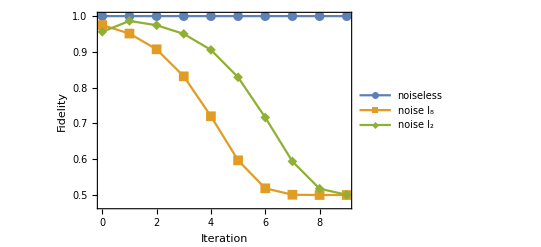

```mathematica
ListPlot[{F U1,F U1I2,F U1I8},Frame->True,FrameLabel->{"Iteration","Fidelity"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},ImageSize->400,PlotRange->All,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Medium},Joined->True,PlotLegends->Placed[{"noiseless",Subscript["I","8"]"noise",Subscript["I","2"]"noise"},{{0.7,0.3},{0.05,0.01}}],Epilog->{Style[Text["λ = 0.05",{19.7,0.96}],14]}]
```

```mathematica
R=10;

ρ2noise=Table[Block[{ρ0},
ρ0=(1-λ)*Outer[Times, GHZ,cGHZ]+λ/2 NoiseMatrix[8]/.λ->λ′;
Transpose[{(Range[R]-1),cGHZ.Normal[schemeρ[ρ0,U1,#]].GHZ&/@(Range[R]-1)//Chop}]],{λ′,0,1,0.2}];

ρ8noise=Table[Block[{ρ0},
ρ0=(1-λ)*Outer[Times, GHZ,cGHZ]+λ/8 IdentityMatrix[8]/.λ->λ′;
Transpose[{(Range[R]-1),cGHZ.Normal[schemeρ[ρ0,U1,#]].GHZ&/@(Range[R]-1)//Chop}]],{λ′,0,1,0.2}];
```

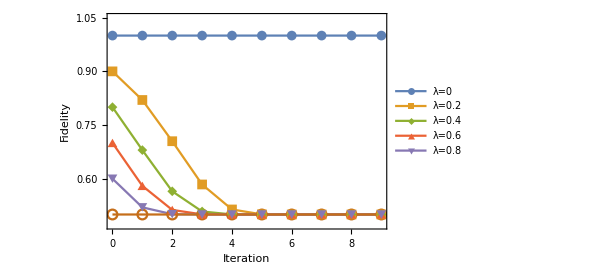

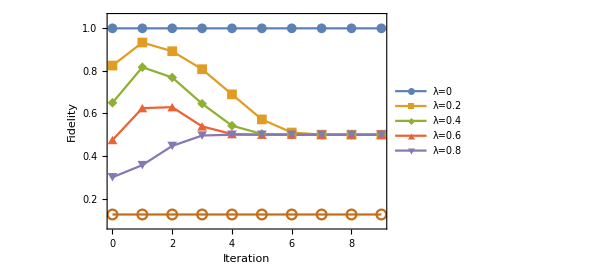

```mathematica
ListPlot[ρ2noise,Frame->True,FrameLabel->{"Iteration","Fidelity"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},ImageSize->440,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Medium},Joined->True,PlotRange->{{0,R-1},{All,1.05}},PlotLegends->Placed[{"λ=0","λ=0.2","λ=0.4","λ=0.6","λ=0.8"},{{0.75,0.15},{0.05,0.01}}],Epilog->{Style[Text["I_2 noise",{20.,0.9977}],14]}]

ListPlot[ρ8noise,Frame->True,FrameLabel->{"Iteration","Fidelity"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},ImageSize->440,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Medium},Joined->True,PlotRange->{{0,R-1},{All,1.05}},PlotLegends->Placed[{"λ=0","λ=0.2","λ=0.4","λ=0.6","λ=0.8"},{{0.75,0.15},{0.05,0.01}}],Epilog->{Style[Text["I_8 noise",{20.,0.9977}],14]}]
```

### U2 unitary

```mathematica
R=10;
ρ02=(1-λ)*ρGHZ+λ/2 NoiseMatrix[8]/.λ->0.05;
ρ08=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->0.05;

F U2=Transpose[{(Range[R]-1),Conjugate[GHZ].Normal[schemeρ[ρGHZ,U2,#]].GHZ&/@(Range[R]-1)//Chop}];
F U2I2=Transpose[{(Range[R]-1),Conjugate[GHZ].Normal[schemeρ[ρ02,U2,#]].GHZ&/@(Range[R]-1)//Chop}];
F U2I8=Transpose[{(Range[R]-1),Conjugate[GHZ].Normal[schemeρ[ρ08,U2,#]].GHZ&/@(Range[R]-1)//Chop}];
```

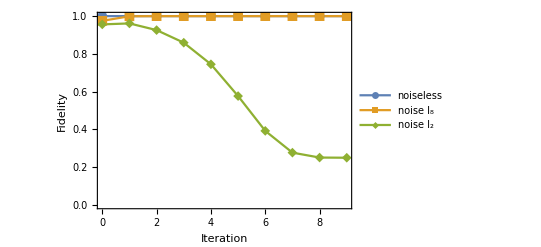

```mathematica
ListPlot[{F U2,F U2I2,F U2I8},Frame->True,FrameLabel->{"Iteration","Fidelity"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},ImageSize->400,PlotRange->All,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Medium},Joined->True,PlotLegends->Placed[{"noiseless",Subscript["I","8"]"noise",Subscript["I","2"]"noise"},{{0.7,0.3},{0.05,0.01}}],Epilog->{Style[Text["λ = 0.05",{19.7,0.96}],14]}]
```

```mathematica
R=10;

ρ2noiseU2=Table[Block[{ρ0},
ρ0=(1-λ)*Outer[Times, GHZ,Conjugate[GHZ]]+λ/2 NoiseMatrix[8]/.λ->λ′;
Transpose[{(Range[R]-1),Conjugate[GHZ].Normal[schemeρ[ρ0,U2,#]].GHZ&/@(Range[R]-1)//Chop}]],{λ′,0,1,0.2}];

ρ8noiseU2=Table[Block[{ρ0},
ρ0=(1-λ)*Outer[Times, GHZ,Conjugate[GHZ]]+λ/8 IdentityMatrix[8]/.λ->λ′;
Transpose[{(Range[R]-1),Conjugate[GHZ].Normal[schemeρ[ρ0,U2,#]].GHZ&/@(Range[R]-1)//Chop}]],{λ′,0,1,0.2}];
```

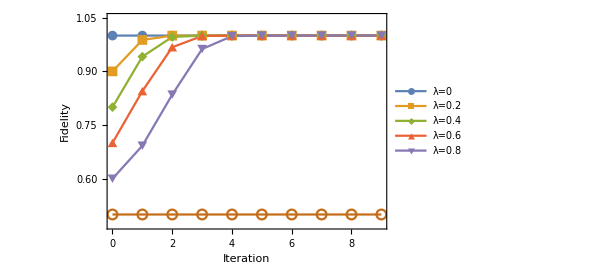

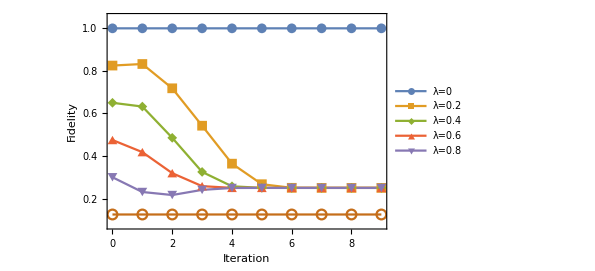

```mathematica
ListPlot[ρ2noiseU2,Frame->True,FrameLabel->{"Iteration","Fidelity"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},ImageSize->440,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Medium},Joined->True,PlotRange->{{0,R-1},{All,1.05}},PlotLegends->Placed[{"λ=0","λ=0.2","λ=0.4","λ=0.6","λ=0.8"},{{0.75,0.15},{0.05,0.01}}],Epilog->{Style[Text["I_2 noise",{20.,0.9977}],14]}]

ListPlot[ρ8noiseU2,Frame->True,FrameLabel->{"Iteration","Fidelity"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},ImageSize->440,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Medium},Joined->True,PlotRange->{{0,R-1},{All,1.05}},PlotLegends->Placed[{"λ=0","λ=0.2","λ=0.4","λ=0.6","λ=0.8"},{{0.75,0.15},{0.05,0.01}}],Epilog->{Style[Text["I_8 noise",{20.,0.9977}],14]}]
```

## Alternating scheme with U1, U2 unitary operators

Throughout the protocol, it has been observed that employing both matrices in an alternating manner yields superior outcomes.
After investigation into the sequence of matrices, it has been determined that the optimal order is to apply U1 followed by U2. This arrangement minimizes the number of state copies required on a physical computer, resulting in more efficient execution.

```mathematica
U2= ({{1/(√2), 0, 0, 1/(√2)}, {1/(√2), 0, 0, -1/(√2)}, {0, 1/(√2), 1/(√2), 0}, {0, 1/(√2), -1/(√2), 0}});
U1={{0,1,0,0},{1,0,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
protρ[rho0_,U1_]:=Block[{ρ,ρ′,UU1},
UU1=KroneckerProduct[U1,U1,U1];
ρ=SparseArray[KroneckerProduct[rho0,rho0]];
ρ′=SparseArray[M].SparseArray[UU1].SparseArray[TRF].ρ.ConjugateTranspose[SparseArray[M].SparseArray[UU1].SparseArray[TRF]];
PartialTrace[ρ′,{2,4,6}]
]

schemeρ[rho0_,U1_,U2_,n_]:=Block[{},Fold[#/Tr[#]&@protρ[#1,#2]&,rho0,Take[Flatten[MapThread[{#1,#2}&,{Table[U1,n],Table[U2,n]}],1],All]]]
```

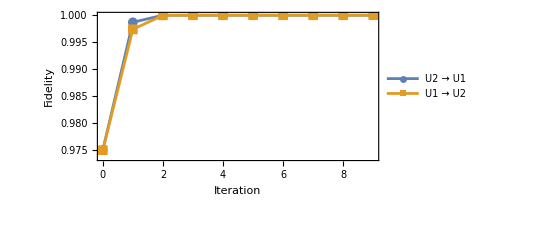

```mathematica
(* sequence of unitaries: U2 -> U1 *)
R=10;
ρ02=(1-λ)*ρGHZ+λ/2 NoiseMatrix[8]/.λ->0.05;

F 1=Transpose[{(Range[R]-1),cGHZ.Normal[schemeρ[ρ02,U2,U1,#]].GHZ&/@(Range[R]-1)//Chop}];
F 2=Transpose[{(Range[R]-1),cGHZ.Normal[schemeρ[ρ02,U1,U2,#]].GHZ&/@(Range[R]-1)//Chop}];

ListPlot[{F 1,F 2},Frame->True,FrameLabel->{"Iteration","Fidelity"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},ImageSize->400,PlotRange->All,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Medium},Joined->True,PlotLegends->Placed[{"U2 → U1","U1 → U2"},{{0.08,0.1},{0.05,0.01}}],Epilog->{Style[Text["λ = 0.05",{6,0.96}],14]}]
```

```mathematica
(* investigating which type of noise can be corrected *)
R=8;
ρ02=(1-λ)*ρGHZ+λ/2 NoiseMatrix[8]/.λ->0.05;
ρ08=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->0.05;

F combI=Transpose[{(Range[R]-1),cGHZ.Normal[schemeρ[ρGHZ,U2,U1,#]].GHZ&/@(Range[R]-1)//Chop}];
F comb2=Transpose[{(Range[R]-1),cGHZ.Normal[schemeρ[ρ02,U2,U1,#]].GHZ&/@(Range[R]-1)//Chop}];
F comb8=Transpose[{(Range[R]-1),cGHZ.Normal[schemeρ[ρ08,U2,U1,#]].GHZ&/@(Range[R]-1)//Chop}];
```

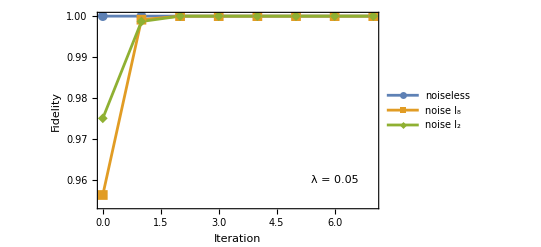

```mathematica
ListPlot[{F combI,F comb8,F comb2},Frame->True,FrameLabel->{"Iteration","Fidelity"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},ImageSize->400,PlotRange->All,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Medium},Joined->True,PlotLegends->Placed[{"noiseless",Subscript["I","8"]"noise",Subscript["I","2"]"noise"},{{0.08,0.1},{0.05,0.01}}],Epilog->{Style[Text["λ = 0.05",{6,0.96}],14]}]
```

```mathematica
(* how strong noise can be corrected *)
R=6;
F8noi=Table[Block[{ρ0},
ρ0=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->λ′;
Transpose[{(Range[R]-1),cGHZ.Normal[schemeρ[ρ0,U1,U2,#]].GHZ&/@(Range[R]-1)//Chop}]],{λ′,0,1,0.2}];
```

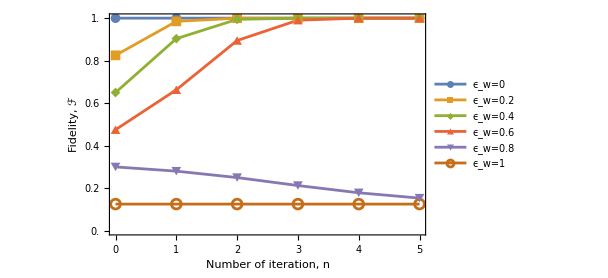

```mathematica
MixedPlot=ListPlot[F8noi,
Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},
LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},
ImageSize->450,Axes->False,FrameStyle->Directive[Black],
PlotMarkers->{Automatic,Medium},Joined->True,PlotRange->All, 
PlotLegends->Placed[PointLegend[{"ϵ_w=0","ϵ_w=0.2","ϵ_w=0.4","ϵ_w=0.6","ϵ_w=0.8", "ϵ_w=1"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},LegendFunction->(Framed[#,Background->White]&)],{{0.8,0.17},{0.15,0.01}}],
FrameTicks->{{Range[0,1,0.2],None},{Range[R]-1,None}}
]
```

```mathematica
(* how many copies of initial GHZ do we need to have one noisefree GHZ *)
1/(Tr[protρ[ρGHZ, Ughz]]*Tr[protρ[ρGHZ, Ughz]]*Tr[protρ[ρGHZ, Ustab]]) (** 100X shots -> 3.125 good events **)
```

32.

```mathematica
100/32//N
```

3.125

```mathematica
(* in this sense better sequence: U1 -> U2 *)
Tr[protρ[ρGHZ, U2]]
Tr[protρ[ρGHZ, U1]]
```

0.25

0.5

### GHZ-like initial state

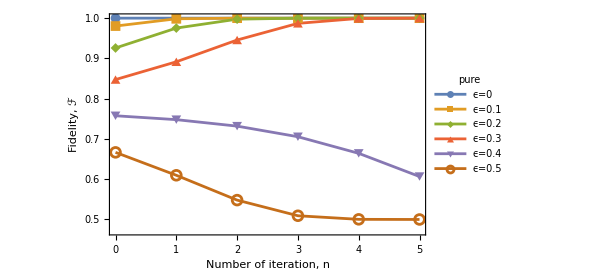

```mathematica
(* alternating scheme works for noisy GHZ-like initial state as well *)

(*Tuples[{0,1},3],
Flatten[KroneckerProduct[S0,S0,S0]]+Flatten[KroneckerProduct[S0,S0,S1]]*)

GHZL=Normalize[N@(GHZ+λ {0,1,0,0,0,0,1,0})];
ρGHZL=SparseArray@Outer[Times, GHZL,Conjugate[GHZL]];

R=6;
F 1=Table[Block[{ρ0,GHZL},
GHZL=Normalize[N@(GHZ+λ {0,1,0,0,0,0,1,0})]/.λ->λ′;
ρ0=SparseArray@Outer[Times, GHZL,Conjugate[GHZL]];
Transpose[{(Range[R]-1),cGHZ.Normal[schemeρ[ρ0,U1,U2,#]].GHZ&/@(Range[R]-1)//Chop}]],{λ′,0,0.5,0.1}];

PurePlot=ListPlot[F 1,Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},
LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},
ImageSize->450,PlotRange->All,Axes->False,FrameStyle->Directive[Black],
PlotMarkers->{Automatic,Medium},Joined->True,
FrameTicks->{{Automatic,None},{Range[R]-1,None}},
PlotLegends->Placed[PointLegend[{"ϵ=0","ϵ=0.1","ϵ=0.2","ϵ=0.3","ϵ=0.4", "ϵ=0.5"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},LegendLabel->"pure",LegendFunction->(Framed[#,Background->White]&)],{{0.8,0.17},{0.15,0.01}}]
]
```

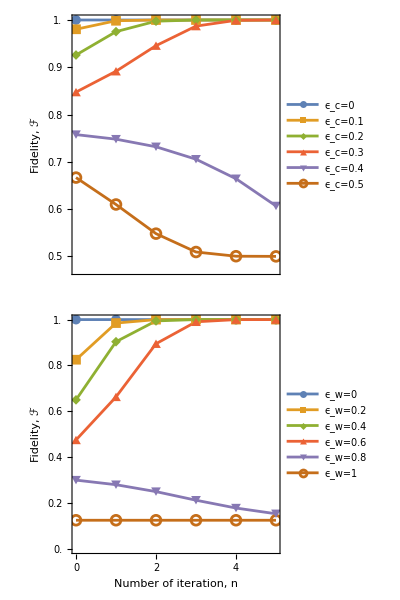

```mathematica
PurePlot2=ListPlot[F 1,Frame->True,FrameLabel->{None,"Fidelity, ℱ"},
LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},
ImageSize->450,PlotRange->All,Axes->False,FrameStyle->Directive[Black],
PlotMarkers->{Automatic,Medium},Joined->True,
FrameTicks->{{Range[0.5,1,0.1],None},{None,None}},
PlotLegends->Placed[PointLegend[{"ϵ_c=0","ϵ_c=0.1","ϵ_c=0.2","ϵ_c=0.3","ϵ_c=0.4", "ϵ_c=0.5"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},LegendFunction->(Framed[#,Background->White]&)],{{0.8,0.17},{0.15,0.01}}]
];

Grid[{{PurePlot2},{ MixedPlot}},Alignment->Left, Spacings->{0,-0.1}]
```

## Measurement error

In this section, a classical readout measurement error has been introduced. There is a probability p of obtaining a measurement outcome of ‘1’ instead of ‘0’, while there is a probability of 1-p for the correct readout.
It has been discovered that there exists a threshold p_tres, such that for values below this threshold, every scenario converges to a pure GHZ state with a fidelity of 1.

```mathematica
(* Measurement projectors *)
M0=Outer[Times, {1,0},Conjugate[{1,0}]];
M1=Outer[Times, {0,1},Conjugate[{0,1}]];

(* readout measurement scenarios *)
configs=Flatten[Table[KroneckerProduct@@{Ι,x,Ι,x′,Ι,x″},{x,{M0,M1}},{x′,{M0,M1}},{x″,{M0,M1}}],2];
(* corresponding error rates *)
rates=Flatten[Table[p′*p″*p′″,{p′,{(1-p),p}},{p″,{(1-p),p}},{p′″,{(1-p),p}}]];
(* measurement error *)
M error=Total[MapThread[#1*#2&,{rates,configs}]];

(* protocol *)
protρ[rho0_,U1_,p′_,n_]:=Block[{ρ,ρ′,UU1,Meas},
UU1=KroneckerProduct[U1,U1,U1];
Meas=M error/.p->p′;
ρ=SparseArray[KroneckerProduct[rho0,rho0]];
ρ′=SparseArray[Meas].SparseArray[UU1].SparseArray[TRF].ρ.ConjugateTranspose[SparseArray[Meas].SparseArray[UU1].SparseArray[TRF]];
PartialTrace[ρ′,{2,4,6}]
]

(* protocol v2 *)
protρ[rho0_,U1_,p′_,n_]:=Block[{ρ,ρ′,ρ′′,UU1,Meas},
UU1=KroneckerProduct[U1,U1,U1];
Meas=M error/.p->p′;
ρ=SparseArray[KroneckerProduct[rho0,rho0]];
ρ′=SparseArray[UU1].SparseArray[TRF].ρ.ConjugateTranspose[SparseArray[UU1].SparseArray[TRF]];
ρ′′=SparseArray[Meas].ρ′;
PartialTrace[ρ′′,{2,4,6}]
]

schemeρ[rho0_,U1_,p′_,n_]:=Block[{},Fold[#/Tr[#]&@protρ[#1,U1,p′,#2]&,rho0,Range[n]]]


(* protocol for alternating U's *)
AltUprot[rho0_,U1_,p′_]:=Block[{ρ,ρ′,UU1,Meas},
UU1=KroneckerProduct[U1,U1,U1];
Meas=M error/.p->p′;
ρ=SparseArray[KroneckerProduct[rho0,rho0]];
ρ′=SparseArray[Meas].SparseArray[UU1].SparseArray[TRF].ρ.ConjugateTranspose[SparseArray[UU1].SparseArray[TRF]];
PartialTrace[ρ′,{2,4,6}]
]

AltScheme[rho0_,U1_,U2_,p′_,n_]:=Block[{},Fold[#/Tr[#]&@AltUprot[#1,#2,p′]&,rho0,Flatten[MapThread[{#1,#2}&,{Table[U1,n],Table[U2,n]}],1]]]
```

```mathematica
R=6;
F8mea=Table[Block[{ρ0},
ρ0=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->0.2;
Transpose[{(Range[R]-1),cGHZ.Normal[AltScheme[ρ0,U1,U2,i,#]].GHZ&/@(Range[R]-1)//Chop}]],{i,0,0.3,0.1}];
```

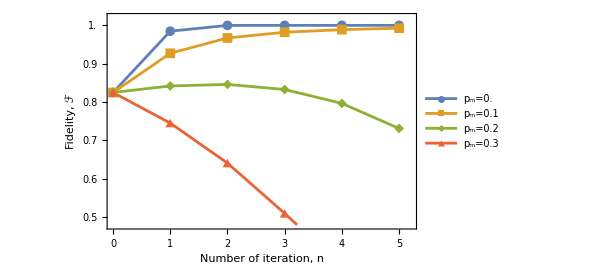

```mathematica
ListPlot[F8mea,
Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},
LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},
ImageSize->440,Axes->False,FrameStyle->Directive[Black],
PlotMarkers->{Automatic,Medium},Joined->True,
FrameTicks->{{Range[0.5,1,0.1],None},{Range[R]-1,None}},
PlotRange->{{0,R-0.8},{0.48,1.02}}, 
PlotLegends->Placed[PointLegend[{"p_m=0.","p_m=0.1","p_m=0.2","p_m=0.3"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},LegendFunction->(Framed[#,Background->White]&)],{{0.8,0.055},{0.25,0.01}}]
]
```

```mathematica
R=15;
F8mea=Table[Block[{ρ0},
ρ0=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->0.3;
Transpose[{(Range[R]-1),cGHZ.Normal[AltScheme[ρ0,U2,U1,i,#]].GHZ&/@(Range[R]-1)//Chop}]],{i,0,0.3,0.05}];
```

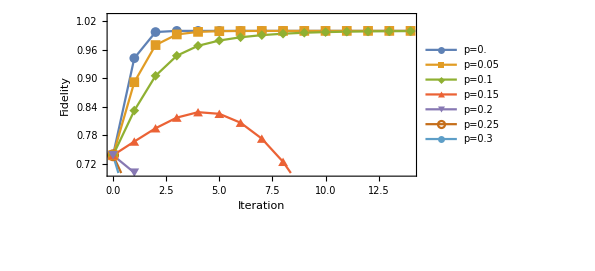

```mathematica
ListPlot[F8mea,Frame->True,FrameLabel->{"Iteration","Fidelity"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},ImageSize->440,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Medium},Joined->True,PlotRange->{{0,R-1},{0.7,1.03}}, PlotLegends->Placed[{"p=0.","p=0.05","p=0.1","p=0.15","p=0.2", "p=0.25","p=0.3"},{{0.78,0.1},{0.05,0.01}}],Epilog->{Style[Text["I_8 noise",{8.,0.26}],14]}]
```

## Gate noise

Furthermore, we introduced noise for the unitary operation by incorporating a 2-qubit depolarization channel.
The depolarization effect acts independently on each of the three unitaries, but with the same probability p_dep.

```mathematica
(*****************************************)
(**** DEPOLARIZATION NOISE OF UNITARY ****)
(*****************************************)

(* gate depolarization *)
Kraus=Flatten[Table[KroneckerProduct@@{bit1,bit2},{bit1,{Ι,X,Y,Z}},{bit2,{Ι,X,Y,Z}}],1];
(* corresponding error rates *)
DRates={Sqrt[1-p]}~Join~Table[Sqrt[p/15],{15}];

Kr1=SparseArray[KroneckerProduct[#,IdentityMatrix[4],IdentityMatrix[4]]&/@Kraus];
Kr2=SparseArray[KroneckerProduct[IdentityMatrix[4],#,IdentityMatrix[4]]&/@Kraus];
Kr3=SparseArray[KroneckerProduct[IdentityMatrix[4],IdentityMatrix[4],#]&/@Kraus];
```

```mathematica
(* protocol for alternating U's *)
NoisyProt[rho0_,U1_,p′_]:=Block[{p=p′,ρ,ρ′,dρ1,dρ2,dρ3,ρM,UU1},
UU1=SparseArray[KroneckerProduct[U1,U1,U1]];
ρ=SparseArray[KroneckerProduct[rho0,rho0]];
ρ′=UU1.SparseArray[TRF].ρ.ConjugateTranspose[UU1.SparseArray[TRF]];
dρ1=Total[MapThread[#1*#2.ρ′.ConjugateTranspose[#1*#2]&,{DRates,Kr1}]];
dρ2=Total[MapThread[#1*#2.dρ1.ConjugateTranspose[#1*#2]&,{DRates,Kr2}]];
dρ3=Total[MapThread[#1*#2.dρ2.ConjugateTranspose[#1*#2]&,{DRates,Kr3}]];
ρM=SparseArray[M].dρ3;
PartialTrace[ρM,{2,4,6}]
]

NoisyScheme[rho0_,U1_,U2_,p′_,n_]:=Block[{},Fold[#/Tr[#]&@NoisyProt[#1,#2,p′]&,rho0,Flatten[MapThread[{#1,#2}&,{Table[U1,n],Table[U2,n]}],1]]]
```

```mathematica
R=6;
F8dep=Table[Block[{ρ0},
ρ0=SparseArray[(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->0.2];
Transpose[{(Range[R]-1),SparseArray[cGHZ].NoisyScheme[ρ0,SparseArray[U1],SparseArray[U2],i,#].SparseArray[GHZ]&/@(Range[R]-1)}]],{i,0,0.08,0.02}];
```

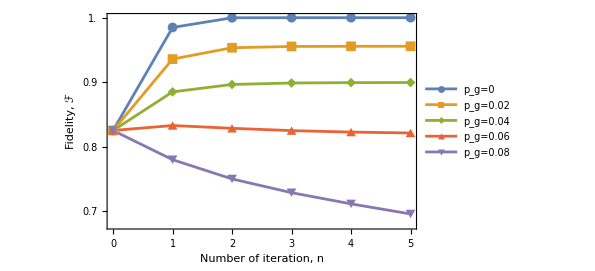

```mathematica
ListPlot[F8dep,
Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},
LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},
ImageSize->440,Axes->False,FrameStyle->Directive[Black],
PlotMarkers->{Automatic,Medium},Joined->True,
PlotRange->All, 
PlotLegends->Placed[PointLegend[{"p_g=0","p_g=0.02","p_g=0.04","p_g=0.06","p_g=0.08"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},LegendFunction->(Framed[#,Background->White]&)],{{0.8,0.09},{0.3,0.01}}],
FrameTicks->{{Range[0.6,1,0.05],None},{Range[R]-1,None}}
]
```

## Analytical evolution of ρ(ϵ) = (1-ϵ)*ρ_0 + ϵ*ρ_error

We conducted an analytical investigation to determine if the protocol is effective for arbitrary errors. It has been discovered that the protocol effectively mitigates the error, reducing it to the order of ε^2 after two iterations when using the sequence U1 followed by U2 (or reversed sequence).

```mathematica
protρϵ[rho0_,U1_]:=Block[{ρ,ρ′,UU1},
UU1=KroneckerProduct[U1,U1,U1];
ρ=SparseArray[KroneckerProduct[rho0,rho0]];
ρ′=SparseArray[M].SparseArray[UU1].SparseArray[TRF].ρ.ConjugateTranspose[SparseArray[UU1].SparseArray[TRF]];
SparseArray[PartialTrace[ρ′,{2,4,6}]]
]

schemeρϵ[rho0_,U1_,U2_,n_]:=Block[{},Fold[#/Tr[#]&@protρϵ[#1,#2]&,rho0,Flatten[MapThread[{#1,#2}&,{Table[U1,n],Table[U2,n]}],1]]]
```

```mathematica
ρerror=Table[ρerror11[i,j],{i,1,8},{j,1,8}];
init=(1-ϵ)*1/2*KroneckerProduct[{1,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,1}]+ϵ*ρerror;
```

```mathematica
iter1=protρϵ[init,U2decomp]/Tr[protρϵ[init,U2decomp]];
out1=Series[iter1,{ϵ,0,1}]//Normal;
```

```mathematica
iter2=Normal[schemeρϵ[init,U2decomp,U1decomp,1]];
out2=Series[iter2,{ϵ,0,1}]//Normal;
```

```mathematica
(*out1//Simplify//MatrixForm*)
out2//Simplify//MatrixForm
```

(1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2)

For a noisy GHZ state, the non-linear transformation proceeds as follows

where the leading order error  reads

### distinct initial copies

If different initial states are used, it has been determined that the protocol is still capable of reducing the error to the order of ε^2 after two iterations when employing the alternating scheme of the protocol.

```mathematica
ρerror11=Table[ρerrore11[i,j],{i,1,8},{j,1,8}];
initial11=(1-ϵ*Tr[ρerror11])*1/2*KroneckerProduct[{1,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,1}]+ϵ*ρerror11;
ρerror22=Table[ρerrore22[i,j],{i,1,8},{j,1,8}];
initial22=(1-ϵ*Tr[ρerror22])*1/2*KroneckerProduct[{1,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,1}]+ϵ*ρerror22;
```

```mathematica
protρϵ12[rho01_,rho02_,U1_,U2_,Ν_]:=Block[{ρ0,ρ0trf,ρ′,ρ′′,UU1,UU2},
UU1=SparseArray[KroneckerProduct[U1,U1,U1]];
UU2=SparseArray[KroneckerProduct[U2,U2,U2]];
ρ0=SparseArray[KroneckerProduct[rho01,rho02]];
ρ0trf=SparseArray[TRF].ρ0.ConjugateTranspose[SparseArray[TRF]];
ρ′=Fold[#/Tr[#]&@(#2.#1.ConjugateTranspose[#2])&,ρ0trf,Flatten[MapThread[{#1,#2}&,{Table[UU1,Ν],Table[UU2,Ν]}],1]];
ρ′′=SparseArray[M].ρ′;
SparseArray[PartialTrace[ρ′′,{2,4,6}]]
]
```

```mathematica
out12=protρϵ12[SparseArray[initial11],SparseArray[initial22],SparseArray[U1decomp],SparseArray[U2decomp],1];
```

```mathematica
out12s=Series[out12,{ϵ,0,1}]//Normal;
%//MatrixForm
```

## No protocol for 1 iteration

```mathematica
initial=ρGHZ+ϵ*(IdentityMatrix[8]/8-ρGHZ)//Normal;
%//MatrixForm
```

(1/2-(3 ϵ)/8 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2-ϵ/2
0 | ϵ/8 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ϵ/8 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ϵ/8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ϵ/8 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ϵ/8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ϵ/8 | 0
1/2-ϵ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2-(3 ϵ)/8)

```mathematica
Tr[IdentityMatrix[8]/8-Normal[ρGHZ]]
```

0

```mathematica
initial={{1/2+ϵ,0,0,0,0,0,0,1/2},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1/2,0,0,0,0,0,0,1/2}};
```

```mathematica
UU=Table[u[i,j],{i,1,4},{j,1,4}];
finalist=Series[schemeρ[initial,UU,1]//Normal,{ϵ,0,1}];
```

```mathematica
feltetel1=SeriesCoefficient[finalist[[1,8]],{ϵ,0,1}]//Simplify;
feltetel2=SeriesCoefficient[finalist[[1,1]],{ϵ,0,1}]//Simplify;
feltetel3=SeriesCoefficient[finalist[[8,1]],{ϵ,0,1}]//Simplify;
feltetel4=SeriesCoefficient[finalist[[1,8]],{ϵ,0,1}]//Simplify;
```

```mathematica
feltetel1//FullSimplify
```

$Aborted

## Uniform protocol with trained unitary matrix

```mathematica
Ut={{1/Sqrt[2] E^(I*ϕ),0,0,1/Sqrt[2] I},{0,1/Sqrt[2],1/Sqrt[2],0},{1/Sqrt[2] I,0,0,1/Sqrt[2] E^(-I*ϕ)},{0,1/Sqrt[2],-(1/Sqrt[2]),0}}/. {ϕ->π/6};
%//MatrixForm
Ut=1/Sqrt[2]*{{ E^(-I*ϕ),0,0,1 },{0,E^(-I*ϕ),1,0},{1,0,0,- E^(I*ϕ)},{0,1,-E^(-I*ϕ),0}}/. {ϕ->π/3};
%//MatrixForm
```

(ⅇ^((ⅈ π)/6)/(√2) | 0 | 0 | ⅈ/(√2)
0 | 1/(√2) | 1/(√2) | 0
ⅈ/(√2) | 0 | 0 | ⅇ^(-(ⅈ π)/6)/(√2)
0 | 1/(√2) | -1/(√2) | 0)

(ⅇ^(-(ⅈ π)/3)/(√2) | 0 | 0 | 1/(√2)
0 | ⅇ^(-(ⅈ π)/3)/(√2) | 1/(√2) | 0
1/(√2) | 0 | 0 | -ⅇ^((ⅈ π)/3)/(√2)
0 | 1/(√2) | -ⅇ^(-(ⅈ π)/3)/(√2) | 0)

The unitary operator of the pre-trained uniform protocol can be break downed into a simplified form of CNOT followed by a Hadamard operator:

```mathematica
UCXH= KroneckerProduct[HadamardMatrix[2], Ι].CNOT[1->2];
%//MatrixForm
```

(1/(√2) | 0 | 0 | 1/(√2)
0 | 1/(√2) | 1/(√2) | 0
1/(√2) | 0 | 0 | -1/(√2)
0 | 1/(√2) | -1/(√2) | 0)

```mathematica
(* function of: protocol for density matrix *)
protρ[rho0_,U_,n_]:=Block[{UU,ρ,ρ′,ρ″},
UU=KroneckerProduct[U,U,U];(* tensor product of UxUxU *)
ρ=SparseArray[KroneckerProduct[rho0,rho0]];(* tensor product of ρ_original and ρ_flag *)
ρ′=SparseArray[UU].SparseArray[TRF].ρ.ConjugateTranspose[SparseArray[UU].SparseArray[TRF]];(* local unitary operation on transformed basis *)
ρ″=SparseArray[M].ρ′;(* 0-measurment on flag qubits *)
PartialTrace[ρ″,{2,4,6}](* tracing-out flag qubits *)
]
(* function of: iterative application of above protocol*)
schemeρ[rho0_,U_,n_]:=Block[{},Fold[protρ[#1,U,#2]/Tr[protρ[#1,U,#2]]&,rho0,Range[n]]]
```

```mathematica
R=12;
ρ08=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->0.1;
F UtI8=Transpose[{(Range[R]-1),cGHZ.Normal[schemeρ[ρ08,UCXH,#]].GHZ&/@(Range[R]-1)//Chop}];
```

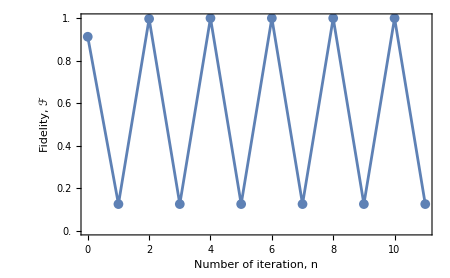

```mathematica
Ptrained=ListPlot[F UtI8,
Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},
LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},
ImageSize->450,Axes->False,FrameStyle->Directive[Black],
PlotMarkers->{Automatic,Medium},Joined->True,PlotRange->All,
FrameTicks->{{Range[0,1,0.2],None},{Range[R]-1,None}}
]
```

```mathematica
R=12;
ρ02=(1-λ)*ρGHZ+λ/2 NoiseMatrix[8]/.λ->0.05;
ρ08=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->0.05;
F Ut=Transpose[{(Range[R]-1),cGHZ.Normal[schemeρ[N[ρGHZ],N[Ut],#]].GHZ&/@(Range[R]-1)//Chop}];
F UtI2=Transpose[{(Range[R]-1),cGHZ.Normal[schemeρ[ρ02,Ut,#]].GHZ&/@(Range[R]-1)//Chop}];
F UtI8=Transpose[{(Range[R]-1),cGHZ.Normal[schemeρ[ρ08,Ut,#]].GHZ&/@(Range[R]-1)//Chop}];
```

```mathematica
F1Even=Take[F Ut,{1,-1,2}];
F2Even=Take[F UtI2,{1,-1,2}];
F8Even=Take[F UtI8,{1,-1,2}];
```

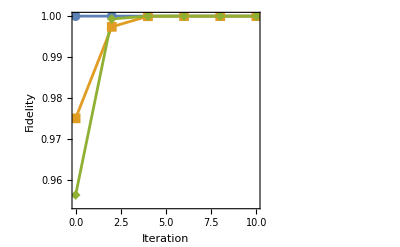

```mathematica
ListPlot[{F1Even, F2Even,F8Even},Frame->True,FrameLabel->{"Iteration","Fidelity"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},ImageSize->400,PlotRange->All,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Medium},Joined->True,Epilog->{Style[Text["λ = 0.05",{19.7,0.96}],14]}]
```

```mathematica
protρ[rho0_,U1_]:=Block[{ρ,ρ′,UU1},
UU1=KroneckerProduct[U1,U1,U1];
ρ=SparseArray[KroneckerProduct[rho0,rho0]];
ρ′=SparseArray[M].SparseArray[UU1].SparseArray[TRF].ρ.ConjugateTranspose[SparseArray[M].SparseArray[UU1].SparseArray[TRF]];
PartialTrace[ρ′,{2,4,6}]
]
schemeρalt[rho0_,U1_,U2_,n_]:=Block[{},Fold[protρ[#1,#2]/Tr[protρ[#1,#2]]&,rho0,Take[Flatten[MapThread[{#1,#2}&,{Table[U1,n],Table[U2,n]}],1],All]]]
```

```mathematica
(* how strong noise can be corrected *)
R=6;
FUtnoi8=Table[Block[{ρ0},
ρ0=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->λ′;
Transpose[{(Range[R]-1),cGHZ.Normal[schemeρalt[ρ0,UCXH,UCXH,#]].GHZ&/@(Range[R]-1)//Chop}]],{λ′,0,1,0.2}];
```

```mathematica
PUtm=ListPlot[FUtnoi8,
Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},
LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},
ImageSize->450,Axes->False,FrameStyle->Directive[Black],
PlotMarkers->{Automatic,Medium},Joined->True,PlotRange->All, 
PlotLegends->Placed[PointLegend[{"ϵ_w=0","ϵ_w=0.2","ϵ_w=0.4","ϵ_w=0.6","ϵ_w=0.8", "ϵ_w=1"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},LegendFunction->(Framed[#,Background->White]&)],{{0.8,0.17},{0.15,0.01}}],
FrameTicks->{{Range[0,1,0.2],None},{Range[R]-1,None}}
]
```

-Graphics-

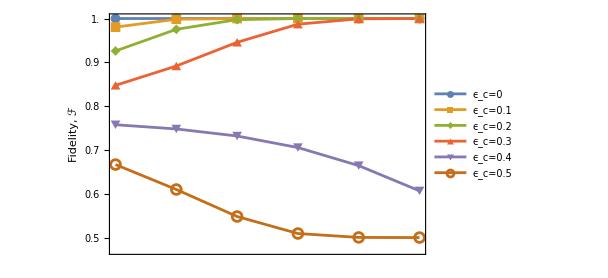

```mathematica
GHZL=Normalize[N@(GHZ+λ {0,1,0,0,0,0,1,0})];
ρGHZL=SparseArray@Outer[Times, GHZL,Conjugate[GHZL]];

R=6;
Ft 1=Table[Block[{ρ0,GHZL},
GHZL=Normalize[N@(GHZ+λ {0,1,0,0,0,0,1,0})]/.λ->λ′;
ρ0=SparseArray@Outer[Times, GHZL,Conjugate[GHZL]];
Transpose[{(Range[R]-1),cGHZ.Normal[schemeρalt[ρ0,UCXH,UCXH,#]].GHZ&/@(Range[R]-1)//Chop}]],{λ′,0,0.5,0.1}];

PUtp=ListPlot[Ft 1,Frame->True,FrameLabel->{None,"Fidelity, ℱ"},
LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},
ImageSize->450,PlotRange->All,Axes->False,FrameStyle->Directive[Black],
PlotMarkers->{Automatic,Medium},Joined->True,
FrameTicks->{{Range[0.5,1,0.1],None},{None,None}},
PlotLegends->Placed[PointLegend[{"ϵ_c=0","ϵ_c=0.1","ϵ_c=0.2","ϵ_c=0.3","ϵ_c=0.4", "ϵ_c=0.5"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},LegendFunction->(Framed[#,Background->White]&)],{{0.8,0.17},{0.15,0.01}}]
]
```

```mathematica
Grid[{{PUtp},{ PUtm}},Alignment->Left, Spacings->{0,-0.1}]
(*Export["/Users/aronrozgonyi/Documents/PhD/alternating_protocol/paper-fig/fig8-cxh.pdf",%]*)
```

-Graphics-

```mathematica
R=6;
Ftmea=Table[Block[{ρ0},
ρ0=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->0.2;
Transpose[{(Range[R]-1),cGHZ.Normal[AltScheme[ρ0,Ut,Ut,i,#]].GHZ&/@(Range[R]-1)//Chop}]],{i,0,0.3,0.1}];
```

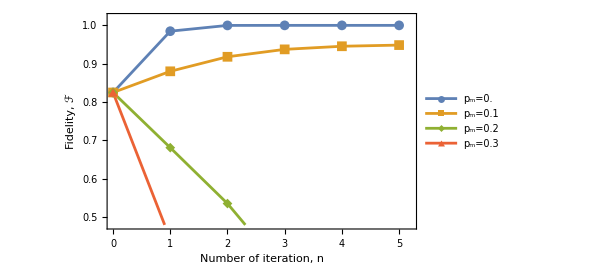

```mathematica
ListPlot[Ftmea,
Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},
LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},
ImageSize->440,Axes->False,FrameStyle->Directive[Black],
PlotMarkers->{Automatic,Medium},Joined->True,
FrameTicks->{{Automatic,None},{Range[R]-1,None}},
PlotRange->{{0,R-0.8},{0.48,1.02}}, 
PlotLegends->Placed[PointLegend[{"p_m=0.","p_m=0.1","p_m=0.2","p_m=0.3"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},LegendFunction->(Framed[#,Background->White]&)],{{0.8,0.055},{0.25,0.01}}]
]
```

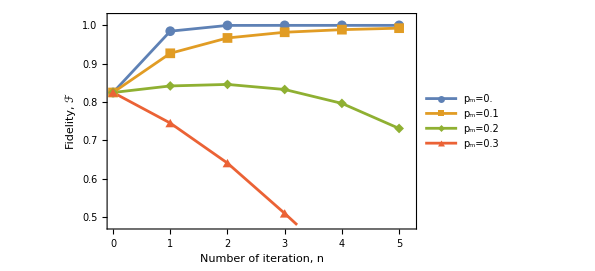

```mathematica
ListPlot[F8mea,
Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},
LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},
ImageSize->440,Axes->False,FrameStyle->Directive[Black],
PlotMarkers->{Automatic,Medium},Joined->True,
FrameTicks->{{Automatic,None},{Range[R]-1,None}},
PlotRange->{{0,R-0.8},{0.48,1.02}}, 
PlotLegends->Placed[PointLegend[{"p_m=0.","p_m=0.1","p_m=0.2","p_m=0.3"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},LegendFunction->(Framed[#,Background->White]&)],{{0.8,0.055},{0.25,0.01}}]
]
```

```mathematica
R=6;
Ftdep=Table[Block[{ρ0},
ρ0=SparseArray[(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->0.2];
Transpose[{(Range[R]-1),SparseArray[cGHZ].NoisyScheme[ρ0,SparseArray[Ut],SparseArray[Ut],i,#].SparseArray[GHZ]&/@(Range[R]-1)}]],{i,0,0.08,0.02}];
```

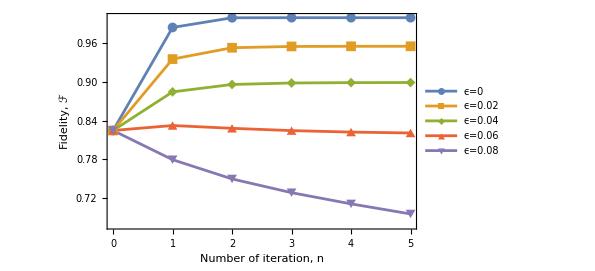

```mathematica
ListPlot[Ftdep,
Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},
LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},
ImageSize->440,Axes->False,FrameStyle->Directive[Black],
PlotMarkers->{Automatic,Medium},Joined->True,
PlotRange->All, 
PlotLegends->Placed[PointLegend[{"ϵ=0","ϵ=0.02","ϵ=0.04","ϵ=0.06","ϵ=0.08"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},LegendFunction->(Framed[#,Background->White]&)],{{0.8,0.09},{0.3,0.01}}],
FrameTicks->{{Automatic,None},{Range[R]-1,None}}
]
```

comparism

```mathematica
F 1//TableForm
Ft 1//TableForm
```

0
1. | 1
1. | 2
1. | 3
1. | 4
1. | 5
1.
0
0.980392 | 1
0.998404 | 2
0.99999 | 3
1. | 4
1. | 5
1.
0
0.925926 | 1
0.975348 | 2
0.997454 | 3
0.999974 | 4
1. | 5
1.
0
0.847458 | 1
0.891589 | 2
0.94569 | 3
0.987064 | 4
0.999314 | 5
0.999998
0
0.757576 | 1
0.747921 | 2
0.731845 | 3
0.705507 | 4
0.664246 | 5
0.606665
0
0.666667 | 1
0.609756 | 2
0.548074 | 3
0.509244 | 4
0.500342 | 5
0.5

0
1. | 1
1. | 2
1. | 3
1. | 4
1. | 5
1.
0
0.980392 | 1
0.998404 | 2
0.99999 | 3
1. | 4
1. | 5
1.
0
0.925926 | 1
0.975348 | 2
0.997454 | 3
0.999974 | 4
1. | 5
1.
0
0.847458 | 1
0.891589 | 2
0.94569 | 3
0.987064 | 4
0.999314 | 5
0.999998
0
0.757576 | 1
0.747921 | 2
0.731845 | 3
0.705507 | 4
0.664246 | 5
0.606665
0
0.666667 | 1
0.609756 | 2
0.548074 | 3
0.509244 | 4
0.500342 | 5
0.5